```mathematica
Needs["NDSolve`FEM`"];
Clear["Global`*"];
```

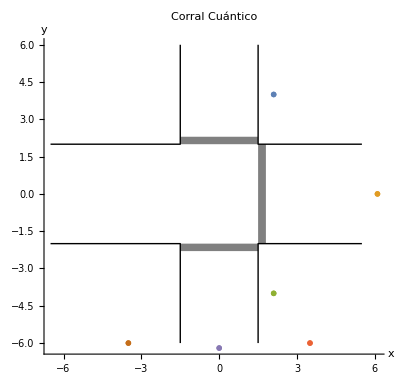

```mathematica
(*************************************************************************************************)
(************************PARÁMETROS A INTRODUCIR POR EL USUARIO****************************************)
V0x=100; (*altura del escalón de potencial en +x*)
V0y=100;(*altura del escalón de potencial en +y*)
V0my=1;(*altura del escalón de potencial en -x*)
k=1.2; (*momento inicial/hbar*)
σ=0.5; (*ancho de la gaussiana*)
(**************************************************)
anchob=0.3; (*ancho de las barreras*)
L1=4;L2=4;L3=4;L4=4;L5=3;L6=5; (*longitudes del corral*)
a=1.5; (*factor de escala de la malla respecto al corral*)
(**************************************************)
PrecEsp=0.5; (*Precisión espacial del FEM*)
PrecTemp=0.5; (*Precisión temporal del FEM*)
tf=6; (*tiempo final*)
tp=0.1; (*tamaño del paso en el tiempo*)
(****************************************************************)

V[x_,y_]:=Piecewise[{{20000,(x≤(-L5/2 )&&y≥( L2/2))||(x≥( L5/2) &&y≥( L2/2))||(x≤(-L5/2)) &&y≤( - L2/2)||(x≥( L5/2) &&y≤(- L2/2))},{V0x,(L5/2≤ x≤ (L5/2+anchob))&&(-L2/2≤ y≤ L2/2)},{V0y,(-L5/2≤ x≤ L5/2)&&(L2/2≤ y≤ (L2/2+anchob))},{V0my,(-L5/2≤ x≤ L5/2)&&((-L2/2-anchob)≤ y≤ -L2/2)}}]; (*potencial*)
Op1=ⅈ*D[U[t,x,y],{t,1}]+(1/2)*Laplacian[U[t,x,y],{x,y}]-V[x,y]*U[t,x,y]; (*ec. de schrodinger, no igualada a cero*)

(*GRAFICAMOS EL CORRAL*)
corralpart1=Line[{{L5/2 ,L2/2 +L1},{L5/2 ,L2/2 },{L5/2  +L4,L2/2 }}];
corralpart2=Line[{{L5/2  +L4,-L2/2 },{L5/2 ,-L2/2 },{L5/2  ,-L2/2 -L3 }}];
corralpart3=Line[{{-L5/2  ,-L2/2 -L3 },{-L5/2 ,-L2/2 },{-L5/2  -L6,-L2/2 }}];
corralpart4=Line[{{-L5/2  -L6,L2/2 },{-L5/2 ,L2/2 },{-L5/2 ,L2/2 +L1}}];
Lmarcas=ListPlot[{{{L5/2 +0.6,L2/2 +L1/2}},{{L5/2 +L4 +0.6,0}},{{L5/2 +0.6,-L2/2 -L3/2}},{{L5/2 +L4/2,-L2/2 - L3}},{{0,-L2/2 - L3-0.2}},{{-L5/2 -L4/2,-L2/2 - L3}}},PlotMarkers->{{"}L1",20},{"}L2",20},{"}L3",20},{"<- L4 ->",20},{"<- L5 ->",20},{"<- L6 ->",20}}];
corralgraf=Graphics[{Thick,corralpart1,Thick,corralpart2,Thick,corralpart3,Thick,corralpart4},PlotLabel->"Corral Cuántico",Axes->True,AxesLabel->{"x","y"}];
barreras=Graphics[{Gray,Rectangle[{-L5/2,-L2/2-anchob},{L5/2,-L2/2}],Gray,Rectangle[{L5/2,-L2/2},{L5/2+anchob,L2/2}],Gray,Rectangle[{-L5/2,L2/2},{L5/2,L2/2+anchob}]}];
Show[corralgraf,Lmarcas,barreras]

(*CREAMOS LA MALLA*)
malla=ToElementMesh[Rectangle[{a(-L5/2 -L6),a(-L2/2-L3)},{a(L5/2+L4),a(L2/2 +L1)}],MaxCellMeasure->PrecEsp]; 

(*CONDICIÓN DE DIRICHLET EN LAS PAREDES DEL CORRAL*)
F1=DirichletCondition[U[t,x,y]==0,(x≤(-L5/2 )&&y≥( L2/2))||(x≥( L5/2) &&y≥( L2/2))||(x≤(-L5/2)) &&y≤( - L2/2)||(x≥( L5/2) &&y≤(- L2/2))]; 

(*CONDICIÓN INICIAL, GAUSSIANA CENTRADA EN (X,Y)=(-L5/2-L6,0) CON MOMENTO INICIAL EN +X*)
CI=Exp[ⅈ*k*x]* (Exp[-((x+L5/2+L6)^2)/(2 σ^2)]/(σ*Sqrt[2Pi]))*(Exp[-((y)^2)/(2 σ^2)]/(σ*Sqrt[2Pi]));
(*CI=Exp[ⅈ*1*y]* (Exp[-(x)^2/2]/Sqrt[Sqrt[π]]);*)
(*CI=Exp[ⅈ*1*y]* (Exp[-(x)^2/2]/Sqrt[Sqrt[π]]*Exp[-(y)^2/2]/Sqrt[Sqrt[π]]-(-L2/2));*)

(*SOL.NÚMERICA DE U*)
SolNU=NDSolveValue[{Op1==0,F1,U[0,x,y]==CI},U,{t,0,tf},{x,y}∈malla,Method->{"FixedStep","StepSize"-> PrecTemp,Method-> "ImplicitRungeKutta"}];
```

```mathematica
(*GRAFICAMOS 2D LA DENSIDAD DE PROBABILIDAD DE U*)
frames=Table[Show[{ContourPlot[Abs[SolNU[t,x,y]]^2,{x,a(-L5/2-L6),a(L5/2 +L4)},{y,a(-L2/2 -L3),a(L2/2 +L1)},ColorFunction-> "TemperatureMap",PlotRange-> All,PlotLabel->"Densidad de Probabilidad",Axes->True,AxesLabel->{"x","y"}],corralgraf,barreras}],{t,0,tf,tp}];
ListAnimate[frames]
```

```mathematica
(*GRAFICAMOS 3D LA DENSIDAD DE PROBABILIDAD DE U*)
frames3D=Table[Plot3D[Abs[SolNU[t,x,y]]^2,{x,a(-L5/2-L6),a(L5/2 +L4)},{y,a(-L2/2 -L3),a(L2/2 +L1)},ColorFunction-> "TemperatureMap",PlotRange-> All,PlotLabel->"Densidad de Probabilidad",Axes->True,AxesLabel->{"y","x","|ψ|^2"}],{t,0,tf,tp}];
ListAnimate[frames3D]
```

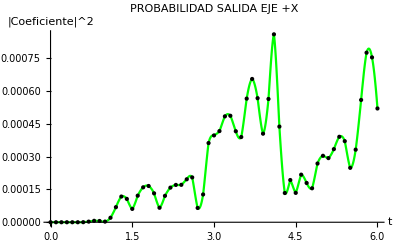

```mathematica
(*CALCULAMOS LAS PROBABILIDADES A LAS SALIDAS DEL CORRAL*)
Coefnu=Table[NIntegrate[Abs[SolNU[t,L4/2+L5/2,y]]^2,{y,-L2/2,L2/2},WorkingPrecision->10,MaxRecursion->20],{t,0,tf,tp}];
time=Table[t,{t,0,tf,tp}];
pointsu=Transpose[{time,Coefnu}];
ifunu= Interpolation[pointsu];
grafu=Plot[ifunu[t],{t,0,tf},Epilog->Point[pointsu],PlotStyle->Green];
Show[grafu,PlotLabel->"PROBABILIDAD SALIDA EJE +X",AxesLabel->{"t","|Coeficiente|^2"}]
```

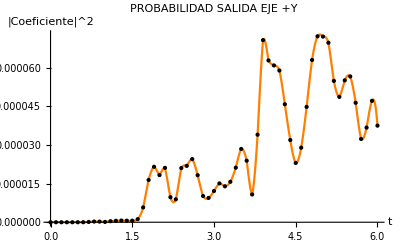

```mathematica
Coefnu2=Table[NIntegrate[Abs[SolNU[t,x,L2/2 +L1/2]]^2,{x,-L5/2,L5/2},WorkingPrecision->10,MaxRecursion->20],{t,0,tf,tp}];
time=Table[t,{t,0,tf,tp}];
pointsu2=Transpose[{time,Coefnu2}];
ifunu2= Interpolation[pointsu2];
grafu2=Plot[ifunu2[t],{t,0,tf},Epilog->Point[pointsu2],PlotStyle->Orange];
Show[grafu2,PlotLabel->"PROBABILIDAD SALIDA EJE +Y",AxesLabel->{"t","|Coeficiente|^2"}]
```

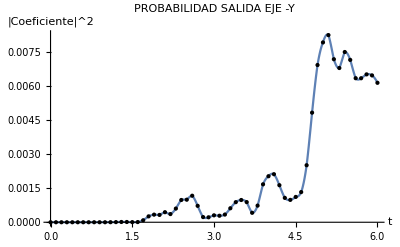

```mathematica
Coefnu3=Table[NIntegrate[Abs[SolNU[t,x,-L2/2 -L3/2]]^2,{x,-L5/2,L5/2},WorkingPrecision->10,MaxRecursion->20],{t,0,tf,tp}];
time=Table[t,{t,0,tf,tp}];
pointsu3=Transpose[{time,Coefnu3}];
ifunu3= Interpolation[pointsu3];
grafu3=Plot[ifunu3[t],{t,0,tf},Epilog->Point[pointsu3]];
Show[grafu3,PlotLabel->"PROBABILIDAD SALIDA EJE -Y",AxesLabel->{"t","|Coeficiente|^2"}]
```

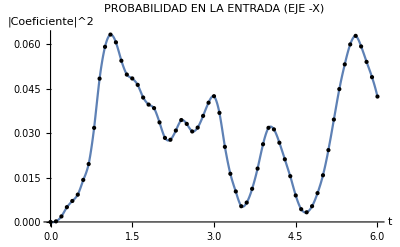

```mathematica
Coefnu4=Table[NIntegrate[Abs[SolNU[t,-L5/2-L6/2,y]]^2,{y,-L2/2,L2/2},WorkingPrecision->10,MaxRecursion->20],{t,0,tf,tp}];
time=Table[t,{t,0,tf,tp}];
pointsu4=Transpose[{time,Coefnu4}];
ifunu4= Interpolation[pointsu4];
grafu4=Plot[ifunu4[t],{t,0,tf},Epilog->Point[pointsu4]];
Show[grafu4,PlotLabel->"PROBABILIDAD EN LA ENTRADA (EJE -X)",AxesLabel->{"t","|Coeficiente|^2"}]
```

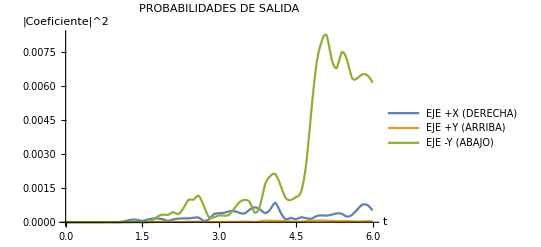

```mathematica
time=Table[t,{t,0,tf,tp}];
Coefnu=Table[NIntegrate[Abs[SolNU[t,L4/2+L5/2,y]]^2,{y,-L2/2,L2/2},WorkingPrecision->10,MaxRecursion->20],{t,0,tf,tp}];
pointsu=Transpose[{time,Coefnu}];
ifunu= Interpolation[pointsu];
Coefnu2=Table[NIntegrate[Abs[SolNU[t,x,L2/2 +L1/2]]^2,{x,-L5/2,L5/2},WorkingPrecision->10,MaxRecursion->20],{t,0,tf,tp}];
pointsu2=Transpose[{time,Coefnu2}];
ifunu2= Interpolation[pointsu2];
Coefnu3=Table[NIntegrate[Abs[SolNU[t,x,-L2/2 -L3/2]]^2,{x,-L5/2,L5/2},WorkingPrecision->10,MaxRecursion->20],{t,0,tf,tp}];
pointsu3=Transpose[{time,Coefnu3}];
ifunu3= Interpolation[pointsu3];

grafs=Plot[{ifunu[t],ifunu2[t],ifunu3[t]},{t,0,tf},PlotLegends-> {"EJE +X (DERECHA)","EJE +Y (ARRIBA)","EJE -Y (ABAJO)"},PlotRange->All];
Show[grafs,PlotLabel->"PROBABILIDADES DE SALIDA",AxesLabel->{"t","|Coeficiente|^2"}]
```